```mathematica
yourFunc=Function[{u,v},Re[Exp[2 π I (8u)]]];

plotted = ParametricPlot3D[{(2+Cos[2 π v]) Sin[2 π u],(2+Cos[2 π v]) Cos[2 π u],Sin[2 π v]},{u,0,1},{v,0,1},MeshFunctions->Function[{x,y,z,u,v},yourFunc[u,v]],Mesh->{{0}},(*Because you state yourFunc[u,v]=0*)MeshStyle->Directive[Blue,Thick],PlotPoints->50]
```

-Graphics3D-

```mathematica
Export["torus.png",plotted, ImageSize-> 72  20]
```

torus.png

```mathematica
Show[%44,ImageSize->Large]
```

```mathematica
Show[%46,Boxed->False]
```

-Graphics3D-

```mathematica
Rasterize[%44,"Image"]
```

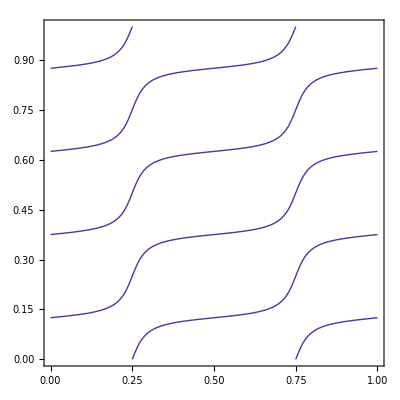

```mathematica
ContourPlot[Re[2 Exp[2 Pi I (x+2y)]+3 Exp[2 Pi I (x-2y)]]== 0, {x,0,1},{y,0,1}]
```

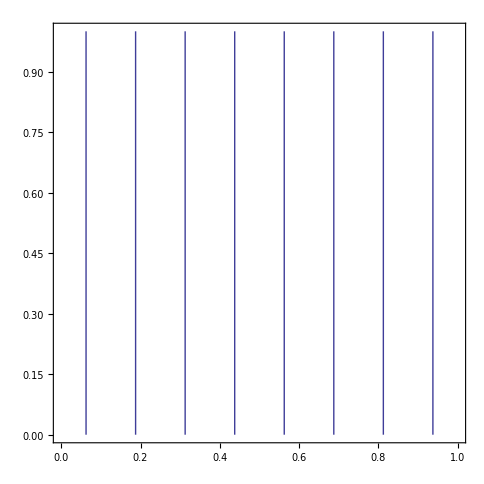

```mathematica
ContourPlot[Re[Exp[2 π I (4 u)]] == 0, {u,0,1},{v,0,1}]
```